### Preamble

```mathematica
(*Variables*)
website = "https://www.northropgrumman.com/";
sentences1 = {{"An apple a day keeps the doctor away", "Apple had a record-breaking quarter", "Put an apple in a pie","An apple is great on salad"},{"Green eggs and ham are tasty","My brother and I are going home now"}};
(*Instantiate NN*)
net=NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"]
elmo=NetFlatten[NetGraph[{net,ThreadingLayer[(#1+#2+#3)/3&]},{Map[NetPort[{1,#}]&,NetInformation[net,"OutputPortNames"]]->2}],1]
MatrixPlot[elmo["Hello world"]];
```

NetGraph[<>]

NetGraph[<>]

### Web Scrape

```mathematica
session=StartWebSession["Chrome", Visible->True];
WebExecute[session, "OpenPage"-> website];
innerText=WebExecute[session, "JavascriptExecute"->"return document.getElementById('content').innerText"]
```

ESPAStar™: A Freight Train to Space
Learn More
Forbes 2022 World’s Best Employers List
Northrop Grumman Recognized for our Legendary Company Culture
Join Us
For some, the word 'impossible' ends discussions. For us, it's a starting point.
Technology and Innovation
Learn More
James Webb Space Telescope
How Northrop Grumman Prepared the Webb Sunshield to Unfold Flawlessly in Space
Learn More

### Text Treatment

```mathematica
(*Convert sentences to string elements in 'sentences'*)
(*Remove commas from 'sentences'*)
(*Delete empty cases from 'sentences'*)
sentences= DeleteCases[StringDelete[#,{",","\"",")","(","-","—","—"}]& /@StringSplit[innerText,{"\n","."}],""];
```

### FeatureSpacePlot

```mathematica
(*Feature Space Plot*)
FeatureSpacePlot[sentences,FeatureExtractor->elmo,LabelingFunction->Callout]
```

-Graphics-

### ColorNet

```mathematica
dr=DimensionReduction[Flatten[elmo[sentences],1],3];
colorNet=NetReplacePart[elmo,"Output"->NetDecoder[{"Function",Function[Map[RGBColor,0.8*LogisticSigmoid[dr[#]]]]}]];
colorNet["The cat is on the mat"];
wordContextColor[sentence_]:=Row[MapThread[Style[#1,#2,Bold]&,{StringSplit[sentence],colorNet[sentence]}],"  "];
wordContextColor/@sentences//TableForm
```

NetDecoder::extfwarn: Specified function Map[«2»]& appears to require definitions of external symbols (, ). Be aware that the definitions and values of these symbols will not be retained if the net is saved using Export, Put, or DumpSave.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of …; dimensions are 6 and 8.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of …; dimensions are 7 and 9.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

Row[MapThread[Style[#1,#2,Bold]&,{{ESPAStar™:,A,Freight,Train,to,Space},{RGBColor[{0.7911014354025748, 0.39185821308087143, 0.7808698589952723}],RGBColor[{0.2500484561198279, 0.4449188011083802, 0.7885232989975406}],RGBColor[{0.03441881901284771, 0.34132449516044067, 0.13386187488776116}],RGBColor[{0.11280925967055798, 0.07656255558464313, 0.05151351074020641}],RGBColor[{0.7998628510069277, 0.04182145732759546, 0.005247509464269607}],RGBColor[{0.7996523815294846, 0.03273875837727771, 0.000170687017017015}],RGBColor[{0.03209862090290816, 0.05733930728670464, 0.0002909177381500688}],RGBColor[{0.7999705102404953, 0.09609474328898047, 0.008930038662587179}]}}],  ]
    LearnMore
Row[MapThread[Style[#1,#2,Bold]&,{{Forbes,2022,World’s,Best,Employers,List},{RGBColor[{0.799939723700401, 0.4115098533722974, 0.7999999976271822}],RGBColor[{0.7970333878860036, 0.6123653810284191, 0.7999999935772348}],RGBColor[{0.7999078157887145, 0.02933445892909245, 0.7999999994817986}],RGBColor[{0.6767237531215592, 0.6659562669287514, 0.7999999946157313}],RGBColor[{0.24781475026047417, 0.7874538309008923, 0.7999999999753972}],RGBColor[{0.7999198779956775, 0.00824549378736261, 0.7999999847727142}],RGBColor[{0.7998964853879315, 0.0007086747159844357, 0.799992611278036}],RGBColor[{0.7757703054981988, 0.007839446474197483, 0.799898331053707}]}}],  ]
    NorthropGrummanRecognizedforourLegendaryCompanyCulture
    JoinUs
Row[MapThread[Style[#1,#2,Bold]&,{{For,some,the,word,'impossible',ends,discussions},{RGBColor[{0.000019410541220258543, 0.2918543502313721, 0.35857070544793324}],RGBColor[{1.077453830594427*^-6, 0.7928305643315516, 0.06400978543348855}],RGBColor[{3.595087362419492*^-6, 0.7989200099278535, 0.015494296150061267}],RGBColor[{7.427703683022987*^-7, 0.7995714255782655, 0.7008406291990777}],RGBColor[{8.264703424576736*^-7, 0.7994355163236397, 0.37833505649698806}],RGBColor[{0.000015527992573922595, 0.7997755047608666, 0.7677911845906993}],RGBColor[{0.000016134424098528246, 0.7989194415271936, 0.45801751306844096}],RGBColor[{1.213915445014968*^-6, 0.7983192502789108, 0.19896242352177926}],RGBColor[{0.00042390009947014003, 0.7273459598110055, 0.4081761714529384}]}}],  ]
Row[MapThread[Style[#1,#2,Bold]&,{{For,us,it's,a,starting,point},{RGBColor[{0.00001088682533873443, 0.24074215373850813, 0.5340622114448726}],RGBColor[{9.199773048071487*^-7, 0.7850308390447818, 0.2495143731761106}],RGBColor[{0.00004716253407614868, 0.7999717023500365, 0.3996524818993423}],RGBColor[{1.891317638869547*^-6, 0.7999018486767578, 0.7964883387747201}],RGBColor[{5.137435296370581*^-7, 0.7998685043355759, 0.7988667846819777}],RGBColor[{2.758563555497061*^-6, 0.7986451618517149, 0.09630322649041617}],RGBColor[{0.00009054371363515854, 0.7929814950315333, 0.28329617649830036}],RGBColor[{0.00015241030161213797, 0.787887678104658, 0.4161836344167495}]}}],  ]
    TechnologyandInnovation
    LearnMore
    JamesWebbSpaceTelescope
    HowNorthropGrummanPreparedtheWebbSunshieldtoUnfoldFlawlesslyinSpace
    LearnMore

# Scratch

```mathematica
features1=FeatureExtract[sentences,elmo];
xy1=DimensionReduce[features1,2,Method->"TSNE"];
ListPlot[xy1->sentences,PlotMarkers->{Automatic, Medium},AxesLabel->None]
```

-Graphics-

```mathematica
ListPlot[xy1->sentences,PlotMarkers->{Automatic, Medium},AxesLabel->None]
```

-Graphics-

```mathematica
sentences
xy1 === Flatten[List/@xy1,1]
```

{ESPAStar™: A Freight Train to Space,Learn More,Forbes 2022 World’s Best Employers List,Northrop Grumman Recognized for our Legendary Company Culture,Join Us,For some the word 'impossible' ends discussions, For us it's a starting point,Technology and Innovation,Learn More,James Webb Space Telescope,How Northrop Grumman Prepared the Webb Sunshield to Unfold Flawlessly in Space,Learn More}

True

```mathematica
xy2=DimensionReduce[features1,3,Method->"TSNE"];
ListPointPlot3D[Flatten[List/@xy2,1]->sentences]
```

-Graphics3D-

```mathematica
xy1//MatrixForm
```

(46.2677 | -152.131
-49.1536 | 581.064
-134.867 | -177.66
23.2634 | -319.845
229.516 | -45.4314
39.8444 | 108.393
-54.9164 | 54.9073
-116.264 | -453.224
-276.85 | 515.412
283.996 | -327.994
120.1 | -249.421
-110.936 | 465.929)

```mathematica
xy1->sentences
```

{{46.2677,-152.131},{-49.1536,581.064},{-134.867,-177.66},{23.2634,-319.845},{229.516,-45.4314},{39.8444,108.393},{-54.9164,54.9073},{-116.264,-453.224},{-276.85,515.412},{283.996,-327.994},{120.1,-249.421},{-110.936,465.929}}→{ESPAStar™: A Freight Train to Space,Learn More,Forbes 2022 World’s Best Employers List,Northrop Grumman Recognized for our Legendary Company Culture,Join Us,For some the word 'impossible' ends discussions, For us it's a starting point,Technology and Innovation,Learn More,James Webb Space Telescope,How Northrop Grumman Prepared the Webb Sunshield to Unfold Flawlessly in Space,Learn More}

```mathematica
ListPlot[xy1->sentences,PlotMarkers->{Automatic, Medium},AxesLabel->None]
```

-Graphics-

```mathematica
xy1->sentences
```

{{46.2677,-152.131},{-49.1536,581.064},{-134.867,-177.66},{23.2634,-319.845},{229.516,-45.4314},{39.8444,108.393},{-54.9164,54.9073},{-116.264,-453.224},{-276.85,515.412},{283.996,-327.994},{120.1,-249.421},{-110.936,465.929}}→{ESPAStar™: A Freight Train to Space,Learn More,Forbes 2022 World’s Best Employers List,Northrop Grumman Recognized for our Legendary Company Culture,Join Us,For some the word 'impossible' ends discussions, For us it's a starting point,Technology and Innovation,Learn More,James Webb Space Telescope,How Northrop Grumman Prepared the Webb Sunshield to Unfold Flawlessly in Space,Learn More}

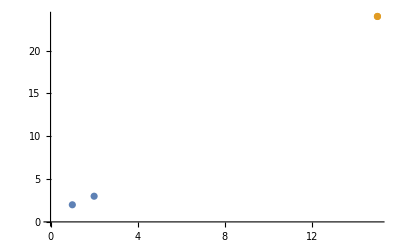

```mathematica
ListPlot[
{
{{1,2},{2,3}},{{3,4}{5,6}}
}
]
```

```mathematica
xy1
```

{{46.2677,-152.131},{-49.1536,581.064},{-134.867,-177.66},{23.2634,-319.845},{229.516,-45.4314},{39.8444,108.393},{-54.9164,54.9073},{-116.264,-453.224},{-276.85,515.412},{283.996,-327.994},{120.1,-249.421},{-110.936,465.929}}

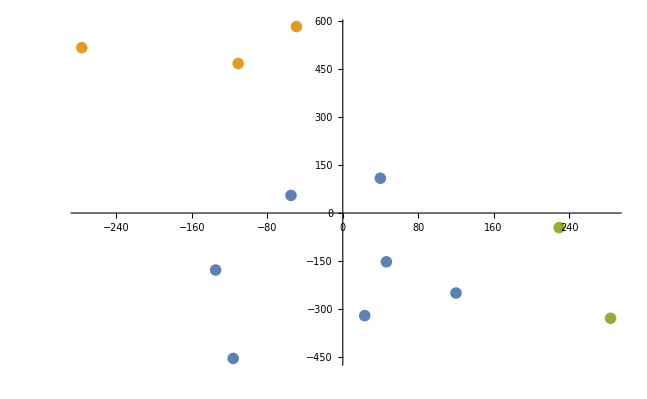

```mathematica
ListPlot[FindClusters[xy1,3, Method->"KMeans"]]
```

```mathematica
EuclideanDistance[{1,2,3,4},{3,2,4,4}]//N
```

2.23607